```mathematica
(* Here I am solving the ODE d^2 u[x]/d x^2 == f[x] *)
```

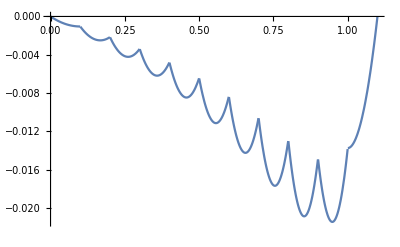

```mathematica
Block[
{f,k,m,n=10,Λ,b,v,x,u},
f[x_]:=x+x^3;
v=Table[Piecewise[{{-n^2(x-(k-1)/n)(x-(k+1)/n),(k-1)/n≤x≤(k+1)/n},{0,True}}],{k,1,n}];
Λ=Table[Table[Integrate[-D[v[[k]],x]D[v[[m]],x],{x,(k-1)/n,(k+1)/n}],{m,1,n}],{k,1,n}];
b=Table[Integrate[f[x]v[[k]],{x,(k-1)/n,(k+1)/n}],{k,1,n}];
u=Inverse[Λ].b;
Plot[Sum[u[[k]]v[[k]],{k,1,n}],{x,0,1+1/n}]
]
```

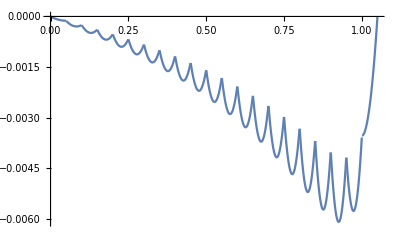

```mathematica
Block[
{f,k,m,n=20,Λ,b,v,x,u},
f[x_]:=x+x^3;
v=Table[Piecewise[{{-n^2(x-(k-1)/n)(x-(k+1)/n),(k-1)/n≤x≤(k+1)/n},{0,True}}],{k,1,n}];
Λ=Table[Table[Integrate[-D[v[[k]],x]D[v[[m]],x],{x,(k-1)/n,(k+1)/n}],{m,1,n}],{k,1,n}];
b=Table[Integrate[f[x]v[[k]],{x,(k-1)/n,(k+1)/n}],{k,1,n}];
u=Inverse[Λ].b;
Plot[Sum[u[[k]]v[[k]],{k,1,n}],{x,0,1+1/n}]
]
```

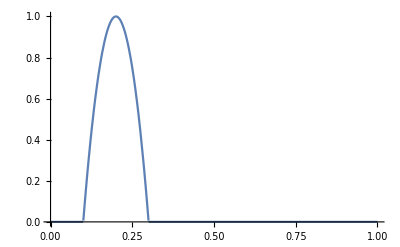

```mathematica
Block[
{n=10,k=2},
Plot[Piecewise[{{-n^2(x-(k-1)/n)(x-(k+1)/n),(k-1)/n≤x≤(k+1)/n},{0,True}}],{x,0,1},PlotRange->{{0,1},{0,1}}]
]
```

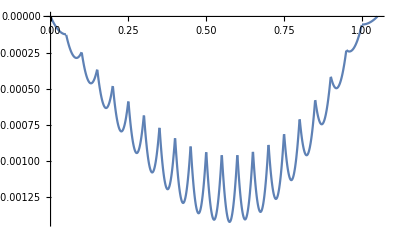

```mathematica
Block[
{f,k,m,n=20,Λ,b,v,x,u},
f[x_]:=x-x^3;
v=Table[Piecewise[{{-n^2(x-(k-1)/n)(x-(k+1)/n),(k-1)/n≤x≤(k+1)/n},{0,True}}],{k,1,n}];
Λ=Table[Table[Integrate[-D[v[[k]],x]D[v[[m]],x],{x,(k-1)/n,(k+1)/n}],{m,1,n}],{k,1,n}];
b=Table[Integrate[f[x]v[[k]],{x,(k-1)/n,(k+1)/n}],{k,1,n}];
u=Inverse[Λ].b;
Plot[Sum[u[[k]]v[[k]],{k,1,n}],{x,0,1+1/n}]
]
```

```mathematica
DSolve[D[u[x],x,x]==x-x^3,u[x],x]
```

{{u[x]→x^3/6-x^5/20+C[1]+x C[2]}}

```mathematica
Solve[1/6-1/20+C[2]==0,C[2]]
```

{{C[2]→-7/60}}

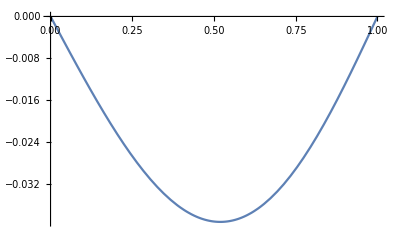

```mathematica
Plot[x^3/6-x^5/20-7/60 x,{x,0,1}]
```

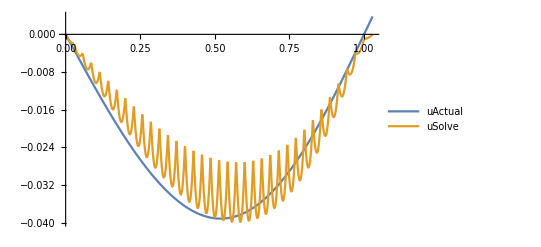

```mathematica
Block[
{f,k,m,n=35,Λ,b,v,x,u},
f[x_]:=x-x^3;
v=Table[Piecewise[{{-n^2(x-(k-1)/n)(x-(k+1)/n),(k-1)/n≤x≤(k+1)/n},{0,True}}],{k,1,n}];
Λ=Table[Table[Integrate[-D[v[[k]],x]D[v[[m]],x],{x,(k-1)/n,(k+1)/n}],{m,1,n}],{k,1,n}];
b=Table[Integrate[f[x]v[[k]],{x,(k-1)/n,(k+1)/n}],{k,1,n}];
u=Inverse[Λ].b;
Plot[{x^3/6-x^5/20-7/60 x,85Sum[u[[k]]v[[k]],{k,1,n}]},{x,0,1+1/n},PlotLegends->{"uActual","uSolve"}]
]
```